```mathematica
ClearAll["Global`*"]
```

```mathematica
t2[r_, t_, i_, s_]:=(i-1)/(2s)t+(s-1)/(2i)r+(r*t)/(4i*s);
t1[r_, t_, i_, s_]:=-2 √(r*t*(2i-r)*(2s-t));
EAM[r_, t_, i_, s_]:=t1[r, t, i, s]+t2[r, t, i ,s];
```

### Contour Plots for EAM

```mathematica
tmax=10;
rmax =10;
cp[f_,rmax_, tmax_,xticks_,yticks_]:=ContourPlot[f[r, t],{r,0,rmax},{t,0,tmax} , Contours->15, FrameStyle->Directive[Black, Thick], FrameLabel->{"r","t"},LabelStyle->{18, Black, FontFamily->"Helvetica"} ,ClippingStyle->Automatic, PlotRange->{{0,rmax},{0,tmax}}, ContourShading->Automatic,PlotLegends->BarLegend[Automatic,6],FrameTicks->{{xticks,None},{yticks,None}}];
shower[f_,p_,minp_,xticks_,yticks_]:=Show[cp[f,2p[[1]],2p[[2]],xticks,yticks], Graphics[{PointSize[Large],Red,Point[minp]}],Graphics[Inset[Framed[Style[StringTemplate["I=`` ; S=``"][p[[1]],p[[2]]],Bold,18,White,FontFamily->"Times New Roman"],BaseStyle->{White, 24}],Scaled[{0.3,0.85}]]]];
```

```mathematica
wslPath="\\\\wsl.localhost\\Ubuntu-24.04\\home\\basavyr\\dev\\mathematica\\mathematica-useful-algorithms\\Physics\\wobbling-scissors-modes\\figures";
```

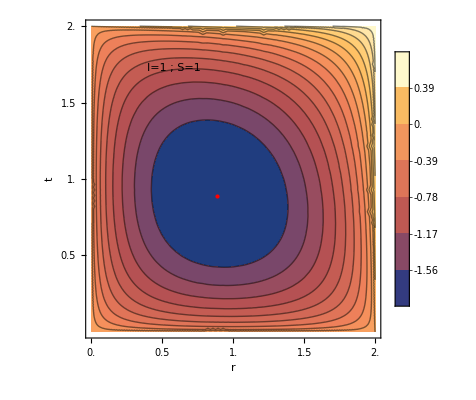

```mathematica
p0={1,1};
min0={0.888889 ,0.888889};
xticks=Table[i,{i,0,2,0.5}];
yticks=Table[i,{i,0.5,2,0.5}];
f0[r_,t_]:=EAM[r, t,p0[[1]],p0[[2]]];
shower[f0, p0,min0,yticks,xticks]
Export[StringTemplate["``\\contour0.png"][wslPath],shower[f0, p0,min0,yticks,xticks], ImageResolution->1200];
Export[StringTemplate["``\\contour0.eps"][wslPath],shower[f0, p0,min0,yticks,xticks], ImageResolution->1200];
```

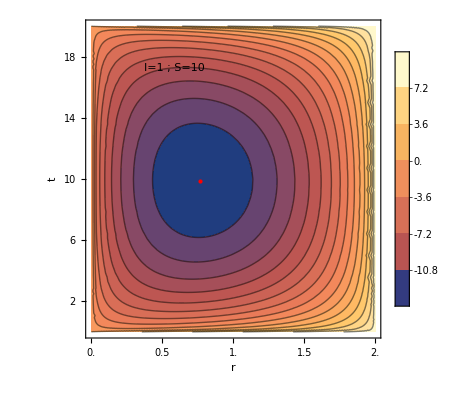

```mathematica
p1={1,10};
min1={0.769031, 9.9012};
xticks=Table[i,{i,0,2,0.5}];
yticks=Table[i,{i,2,20,4}];
f1[r_,t_]:=EAM[r, t,p1[[1]],p1[[2]]];
shower[f1, p1,min1,yticks,xticks]
Export[StringTemplate["``\\contour1.png"][wslPath],shower[f1, p1,min1,yticks,xticks], ImageResolution->1200];
Export[StringTemplate["``\\contour1.eps"][wslPath],shower[f1, p1,min1,yticks,xticks], ImageResolution->1200];
```

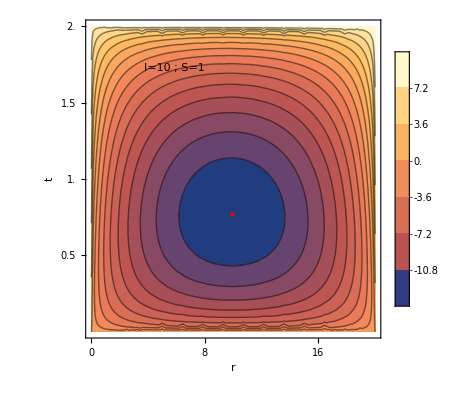

```mathematica
p2={10,1};
min2={9.9012 ,0.769031};
xticks=Table[i,{i,0,20.0,4}];
yticks=Table[i,{i,0.5,2,0.5}];
f2[r_,t_]:=EAM[r, t,p2[[1]],p2[[2]]];
shower[f2, p2,min2,yticks,xticks]
Export[StringTemplate["``\\contour2.png"][wslPath],shower[f2, p2,min2,yticks,xticks], ImageResolution->1200];
Export[StringTemplate["``\\contour2.eps"][wslPath],shower[f2, p2,min2,yticks,xticks], ImageResolution->1200];
```

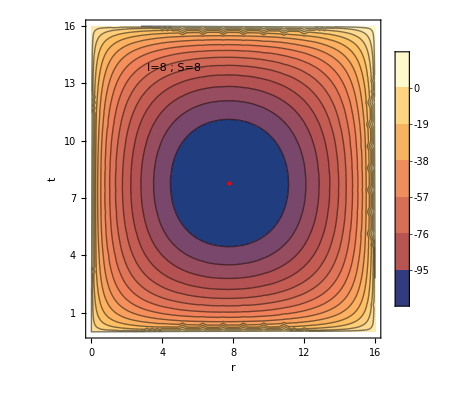

```mathematica
p3={8,8};
min3={7.76608 ,7.76608};
xticks=Table[i,{i,0,17,4}];
yticks=Table[i,{i,1,17,3}];
f3[r_,t_]:=EAM[r, t, p3[[1]],p3[[2]]];
shower[f3, p3,min3,yticks,xticks]
Export[StringTemplate["``\\contour3.png"][wslPath],shower[f3, p3,min3,yticks,xticks], ImageResolution->1200];
Export[StringTemplate["``\\contour3.eps"][wslPath],shower[f3, p3,min3,yticks,xticks], ImageResolution->1200];
```